```mathematica
αcont={0.5135036591175975,0.0023893085927788557}; 
σcont={0.16963079795754127,0.00084757894486039};
ccont={-0.15964102962645102,0.0023730768366581885};
```

### String imaginary part

```mathematica
Integrate[r^3 Sinc[k r],{r,0,rsb}]//FullSimplify
```

(-2+(2-k^2 rsb^2) Cos[k rsb]+2 k rsb Sin[k rsb])/k^4

```mathematica
Limit[Integrate[r^2 Sinc[k r]Exp[-a r],{r,rsb,∞}],a->0]//Simplify
```

(k rsb Cos[k rsb]-Sin[k rsb])/k^3

```mathematica
Vsk[k_,rsb_,σ_]:=4π σ((-2+(2-k^2 rsb^2) Cos[k rsb]+2 k rsb Sin[k rsb])/k^4+rsb(k rsb Cos[k rsb]-Sin[k rsb])/k^3)
```

```mathematica
Imϵk[k_,mD_,T_]:=-π T(k mD^2)/((k^2+mD^2)^2);
```

```mathematica
1/(2 π^2 r)Assuming[{r∈Reals,mD∈Reals,rsb∈Reals,rsb>0,mD>0,r>0},Integrate[k Sin[k r]Vsk[k,rsb,σ]Imϵk[k,mD,T],{k,0,∞}]]
```

$Aborted

```mathematica
ImVs[r_,rsb_,mD_,σ_,T_]:=NIntegrate[(4π)/(2π)^3 k^2 Sinc[k r]Vsk[k,rsb,σ]Imϵk[k,mD,T],{k,0,∞}]
```

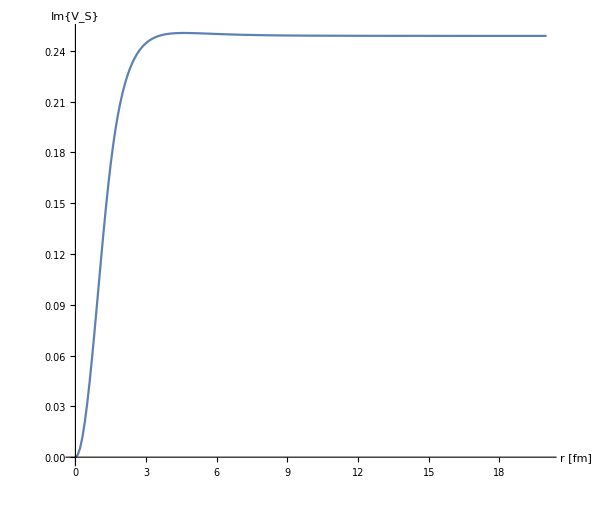

```mathematica
DiscretePlot[-ImVs[r/0.197,1.5/0.197,0.2,σcont[[1]],0.155]+ImVs[0/0.197,1.5/0.197,0.2,σcont[[1]],0.155],{r,0,20,1/10},Joined->True,Filling->None,PlotRange->All,AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},AspectRatio->0.85,AxesLabel->{"r [fm]","Im{V_S}"},ImageSize->{600,600}]
```

### String real part

```mathematica
Reϵk[k_,mD_]:=k^2/(k^2+mD^2);
```

```mathematica
(4π)/(2π)^3 k^2 Sinc[k r]Vsk[k,rsb,σ]Reϵk[k,mD]//FullSimplify
```

(2 σ (-2+2 Cos[k rsb]+k rsb Sin[k rsb]) Sinc[k r])/((k^2+mD^2) π)

```mathematica
ReVsN[r_,rsb_,mD_,σ_,T_]:=NIntegrate[(2 σ (-2+2 Cos[k rsb]+k rsb Sin[k rsb]) Sinc[k r])/((k^2+mD^2) π),{k,0,∞},MaxRecursion->20];
```

```mathematica
Assuming[{σ∈Reals,mD∈Reals,rsb∈Reals,r∈Reals,mD>0,rsb>0,r>0,r>rsb},Integrate[(2 σ (-2+2 Cos[k rsb]+k rsb Sin[k rsb]) Sinc[k r])/((k^2+mD^2) π),{k,0,∞}]]
```

(ⅇ^(-mD r) σ (2-2 Cosh[mD rsb]+mD rsb Sinh[mD rsb]))/(mD^2 r)

```mathematica
Assuming[{σ∈Reals,mD∈Reals,rsb∈Reals,r∈Reals,mD>0,rsb>0,r>0,r<rsb},Integrate[(2 σ (-2+2 Cos[k rsb]+k rsb Sin[k rsb]) Sinc[k r])/((k^2+mD^2) π),{k,0,∞}]]
```

(ⅇ^(-mD r) σ (2+ⅇ^(mD r) (-2+ⅇ^(-mD rsb) (2+mD rsb) Sinh[mD r])))/(mD^2 r)

```mathematica
(ⅇ^(-mD r) σ (2+ⅇ^(mD r) (-2+ⅇ^(-mD rsb) (2+mD rsb) Sinh[mD r])))/(mD^2 r)//FullSimplify
```

(ⅇ^(-mD r) σ (2+ⅇ^(mD r) (-2+ⅇ^(-mD rsb) (2+mD rsb) Sinh[mD r])))/(mD^2 r)

```mathematica
ReVsA[r_,rsb_,mD_,σ_]:=Piecewise[{{(ⅇ^(-mD r) σ (2+ⅇ^(mD r) (-2+ⅇ^(-mD rsb) (2+mD rsb) Sinh[mD r])))/(mD^2 r)+σ rsb-(ⅇ^(-mD rsb) (2+mD rsb+ⅇ^(mD rsb) (-2+mD rsb)) σ)/mD,r<rsb},{(ⅇ^(-mD r) σ (2-2 Cosh[mD rsb]+mD rsb Sinh[mD rsb]))/(mD^2 r)+σ rsb-(ⅇ^(-mD rsb) (2+mD rsb+ⅇ^(mD rsb) (-2+mD rsb)) σ)/mD,r>rsb}}];
```

```mathematica
Assuming[r>rsb,Limit[ReVsA[r,rsb,mD,σ],mD->0]]//Simplify
```

rsb σ

```mathematica
Assuming[r<rsb,Limit[ReVsA[r,rsb,mD,σ],mD->0]]//Simplify
```

r σ

```mathematica
Assuming[r<rsb,Limit[ReVsA[r,rsb,mD,σ],r->0]]//Simplify
```

0

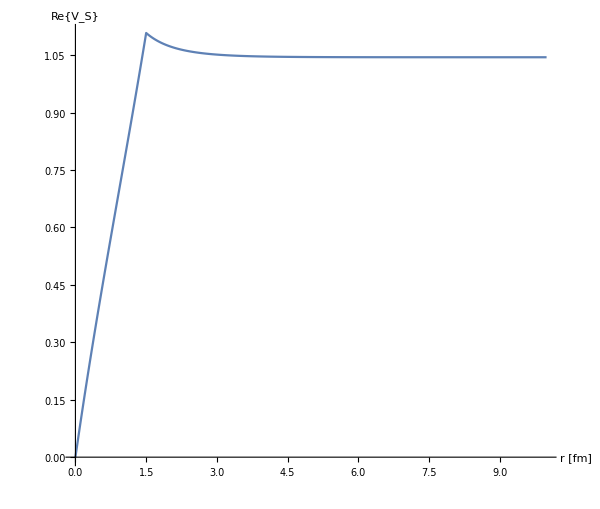

```mathematica
DiscretePlot[ReVsA[r/0.197,1.5/0.197,0.2,σcont[[1]]],{r,10^-10,10,1/100},Joined->True,Filling->None,PlotRange->All,AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},AspectRatio->0.85,AxesLabel->{"r [fm]","Re{V_S}"},ImageSize->{600,600}]
```

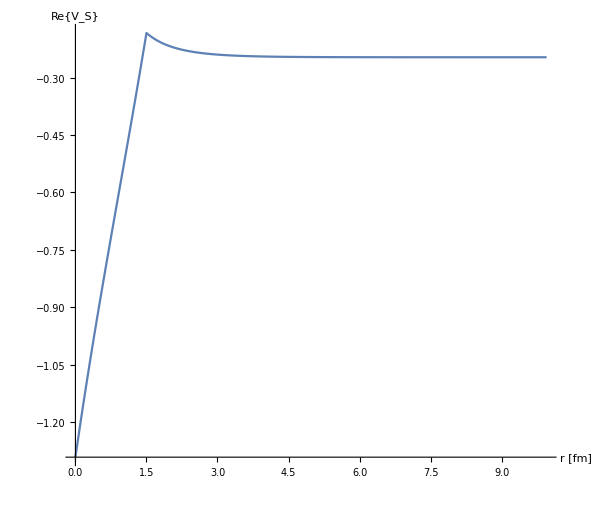

```mathematica
DiscretePlot[ReVsN[r/0.197,1.5/0.197,0.2,σcont[[1]],0.155]-ReVs0,{r,10^-10,10,1/20},Joined->True,Filling->None,PlotRange->All,AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},AspectRatio->0.85,AxesLabel->{"r [fm]","Re{V_S}"},ImageSize->{600,600}]
```

### Full potential

```mathematica
ReVc[r_,mD_,α_,c_]:=-mD α-(ⅇ^(-mD r) α)/r+c;
```

```mathematica
ImVc[r_,mD_,α_,T_]:=T α NIntegrate[(2 z (1-Sinc[mD r z]))/((z^2+1)^2),{z,0,∞},MaxRecursion->20];
```

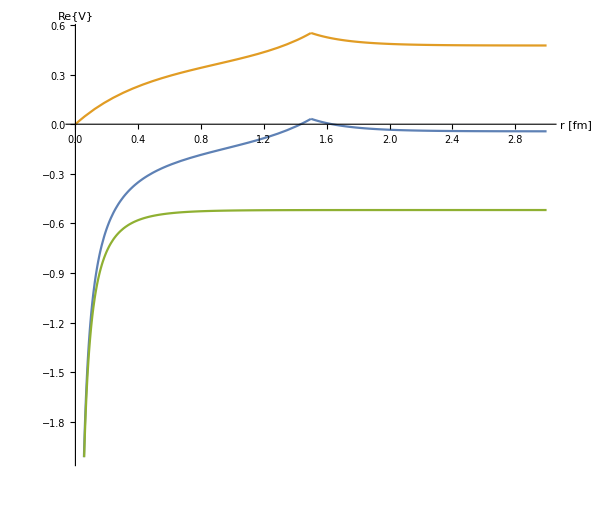

```mathematica
Block[{mD=0.7},Plot[{ReVsA[r/0.197,1.5/0.197,mD,σcont[[1]]]-ReVsA[10^-10,1.5/0.197,mD,σcont[[1]]]+ReVc[r/0.197,mD,αcont[[1]],ccont[[1]]],ReVsA[r/0.197,1.5/0.197,mD,σcont[[1]]]-ReVsA[10^-10,1.5/0.197,mD,σcont[[1]]],ReVc[r/0.197,mD,αcont[[1]],ccont[[1]]]},{r,10^-10,3},AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},AspectRatio->0.85,AxesLabel->{"r [fm]","Re{V}"},ImageSize->{600,600}]]
```

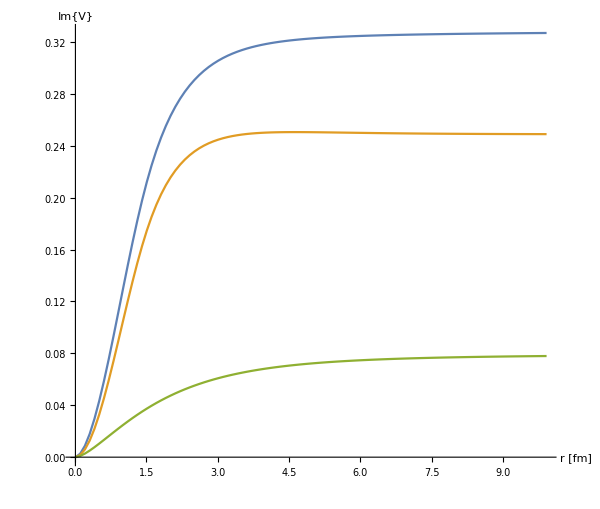

```mathematica
DiscretePlot[{-ImVs[r/0.197,1.5/0.197,0.2,σcont[[1]],0.155]+ImVs[0/0.197,1.5/0.197,0.2,σcont[[1]],0.155]+ImVc[r/0.197,0.2,αcont[[1]],0.155],-ImVs[r/0.197,1.5/0.197,0.2,σcont[[1]],0.155]+ImVs[0/0.197,1.5/0.197,0.2,σcont[[1]],0.155],ImVc[r/0.197,0.2,αcont[[1]],0.155]},{r,1/100,10,1/10},Joined->True,Filling->None,PlotRange->All,AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},AspectRatio->0.85,AxesLabel->{"r [fm]","Im{V}"},ImageSize->{600,600}]
```